# F 5 : Trajectoire et Thermodynamique des acides nucléiques

## 1. Marche aléatoire et Acides nucléiques (SB et DB)

#### A. Construction d’un fragment d’ADN double brin de 10 à 1000 paires de bases.

```mathematica
RandomVariate[NormalDistribution[0,5],{2,2}];
```

```mathematica
Table[RandomVariate[NormalDistribution[0,5],{1}],{x,1,10}]
```

{{-2.89017},{-4.73002},{1.30944},{-7.53286},{-6.9999},{-1.67646},{-2.22242},{-2.8601},{-0.798391},{6.18928}}

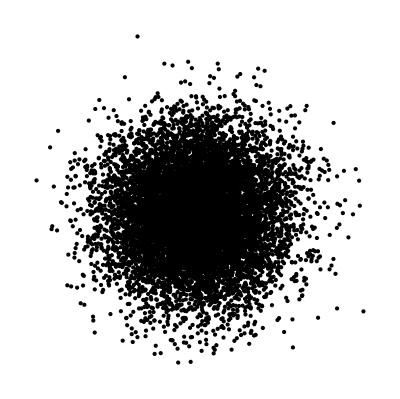

```mathematica
Graphics[{Point[RandomVariate[NormalDistribution[],{10000,2}]]}]
```

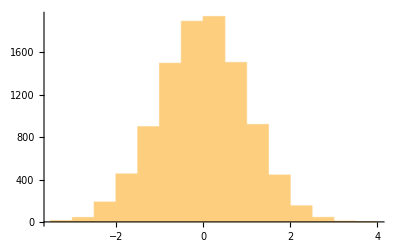

```mathematica
RandomVariate[NormalDistribution[],{10000}]//Histogram
```

```mathematica
nbp= 60;
theta[μ_,σ_,length_]:=RandomVariate[NormalDistribution[μ,σ],{length}];
theta[0Degree,5Degree,nbp]
```

{-0.0867797,0.0190061,0.0332014,0.0174675,0.155675,-0.0584268,-0.17115,-0.127979,0.157188,0.241855,0.0862462,-0.0104864,-0.136957,0.00731326,0.0800113,-0.134393,-0.0197762,-0.0112078,-0.131696,-0.00163955,-0.0566083,0.0830487,0.000224943,-0.037362,0.112899,0.145509,0.0677128,-0.0486612,0.0921324,0.0297751,0.0524084,0.0789637,-0.00846314,-0.0164948,-0.0777195,0.0393164,-0.0407744,-0.126632,0.131396,-0.113056,-0.097337,0.0436665,-0.0765419,-0.055139,0.234242,-0.0158789,0.0778845,-0.184606,-0.115781,0.0701123,0.039785,-0.031465,0.0885867,0.0353252,0.0459575,-0.0127316,0.072393,0.191846,-0.130102,0.0126423}

```mathematica
thetas[μ_,σ_,length_]:=(FoldList[Plus,0,theta[μ,σ,length]]);
```

```mathematica
tiadn[μ_,σ_,length_]:=(Table[{Sin[θ],Cos[θ]},{θ,thetas[μ,σ,length]}]);
```

```mathematica
tjadn[μ_,σ_,length_]:=FoldList[Plus,{0,0},tiadn[μ,σ,length]];
```

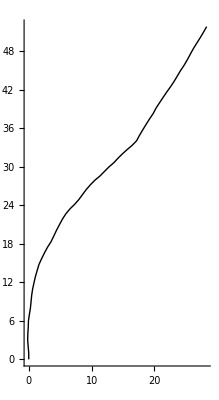

```mathematica
Show[Graphics[Line[tjadn[0Degree,5Degree,nbp]]],Axes->True]
```

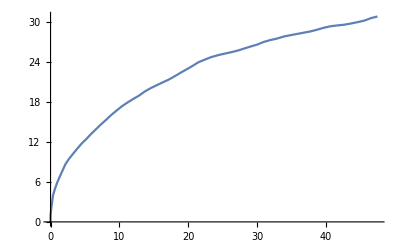

```mathematica
ListPlot[tjadn[0Degree,5Degree,nbp],Joined->True]
```

#### B. Application : Visualisation d’un petit oligonucléotide “quasiment droit”, et “courbes”

```mathematica
tjadnList[μ_,σ_,length_,imax_]:=Table[tjadn[μ,σ,length],{i,imax}];
```

{{{0,0},{0,1},{0.0434642,1.99905},{0.0925401,2.99785},{0.118694,3.99751},{0.219287,4.99244},{0.238803,5.99225},{0.192611,6.99118},{0.196855,7.99117},{0.162871,8.99059},{0.174803,9.99052},{0.27836,10.9851}},{{0,0},{0,1},{0.113149,1.99358},{0.0512835,2.99166},{0.0832406,3.99115},{0.096655,4.99106},{0.146136,5.98984},{0.337429,6.97137},{0.702933,7.90218},{1.08423,8.82663},{1.45183,9.75661},{1.75862,10.7084}}}

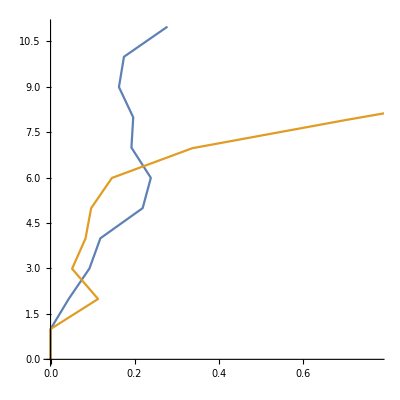

```mathematica
tjs=Table[tjadn[0Degree,5Degree,10],{i,2}]
ListPlot[tjs,AspectRatio->1.,Axes->Automatic,Joined->True]
```

```mathematica
Manipulate[ListPlot[Table[tjadn[0,σ,length],{x}],Joined->True,AspectRatio->1.,Axes->Automatic,PlotRange->{{-nbp/2,nbp/2},{0,nbp}}],{σ,2Degree,10Degree},{length,2,nbp,1},{x,1,100,1}]
```

```mathematica
Manipulate[ListPlot[Table[tjadn[0,σ,length],{x}],Joined->True,AspectRatio->1.,Axes->Automatic,PlotRange->Automatic],{σ,2Degree,20Degree},{length,2},{x,1}]
```

```mathematica
Manipulate[ListPlot[Table[tjadn[0,σ,length],{x}],Joined->True,AspectRatio->1.,Axes->Automatic,PlotRange->Automatic],{σ,5Degree},{length,60},{x,1,100,1}]
```

```mathematica
Manipulate[ListPlot[Table[tjadn[0,σ,length],{x}],Joined->True,AspectRatio->1.,Axes->Automatic,PlotRange->Automatic],{σ,2Degree,20Degree},{length,150},{x,1}]
```

```mathematica
Manipulate[ListPlot[Table[tjadn[0,σ,length],{x}],Joined->True,AspectRatio->1.,Axes->Automatic,PlotRange->Automatic],{σ,4.75Degree},{length,150},{x,1,100,1}]
```

#### À partir de quelle taille peut-on raisonnablement s’attendre à des circularisations ? Discuter

Discusion de voir un cicle à partir de quelle taille ? 
On peut voir le tourne d’un brin comme une marche random dans une dimension suivant la loi uniforme, voir le lengeur comme le chemin de la marche random. 
La distance qu’on veut arriver est 2π, Esperance est 0, le lengeur de chaque pas est la valeur de σ dans le graphe de manipulate
Donc, a partir de (2π)/σ, la probablitié de voir un cicle augmente en suivant loi normal:
Probability[x>2π,x\[Distributed]NormalDistribution[0,σ]]

#### C. Construction de grands ADN

```mathematica
nbp = 10000;
```

```mathematica
Manipulate[ListPlot[Table[tjadn[0,σ,length],{x}],Joined->True,AspectRatio->1.,Axes->Automatic,PlotRange->Automatic],{σ,2Degree,10Degree},{length,100,nbp,100},{x,1,100,1}]
```

```mathematica
Manipulate[ListPlot[Table[tjadn[0,σ,length],{x}],Joined->True,AspectRatio->1.,Axes->Automatic,PlotRange->{{-nbp,nbp},{-nbp,nbp}}],{σ,2Degree,10Degree},{length,100,nbp,100},{x,1,100,1}]
```

```mathematica
sqnbp=2*300 √(nbp/300)//N
```

3464.1

```mathematica
Manipulate[ListPlot[Table[tjadn[0,σ,length],{x}],PlotRange->{{-sqnpb,sqnpb},{-sqnpb,sqnpb}},AspectRatio->1.,Axes->Automatic,Joined->True],{σ,2Degree,10Degree},{length,100,sqnpb,100},{x,1,100,1}]
```

ListPlot::prng: Value of option PlotRange -> {{-sqnpb, sqnpb}, {-sqnpb, sqnpb}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

```mathematica
Manipulate[ListPlot[Table[tjadn[0,σ,length],{x}],PlotRange->{{-sqnpb,sqnpb},{-sqnpb,sqnpb}},AspectRatio->1.,Axes->None,Joined->True],{σ,2Degree,10Degree},{length,100,sqnpb,100},{x,1,100,1}]
```

ListPlot::prng: Value of option PlotRange -> {{-sqnpb, sqnpb}, {-sqnpb, sqnpb}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

## 2. Modification du pK par des interactions ioniques

#### Les acides aminés His 31 et Asp 70 dans le lysozyme T4 sont séparés par 3.5 Å et forment une paire d’ions. Si cette paire est annulée par mutagénèse dirigée (Asp70->Asn70), la stabilité de la protéine est réduite d’environ 12 à 20 kJ/mol.

#### 1./ Calculer l’énergie potentielle coulombienne entre les deux résidus chargés. On supposera que ce sont des charges ponctuelles dans un milieu de constante diélectrique ϵ = 40.

```mathematica
ϵ=40;
```

A + B ---- A.B
A^-+ H^+-- Kd/□ --

#### 2./ Estimer le changement de pK du résidu histidine en supposant que l’énergie de la paire d’ions se reflète intégralement dans l’enthalpie libre δG associée à la perturbation du pK. δG = 2.303*RT δpK, R=8.314 uSI, et T = 300 K.